```mathematica
testSize=All;
imgW=2;
testRNG[r_]:=(
n=Length[r];
drs=Sort[r];
Do[drs[[i]]=drs[[i]]-drs[[i-1]],{i,n,2,-1}];
λ=1/Mean[drs];
walks=Table[Accumulate[2r[[100(i-1)+1;;100i]]-1],{i,1,Floor[n/100]}];
Grid[{
{
ListPlot[r[[1;;If[n>10000,10000,All]]],Joined->False,PlotRange->{All,{0,1}},AspectRatio->1,ImageSize->72*imgW],
Show[Histogram[r,100,"PDF",AspectRatio->1],Plot[PDF[UniformDistribution[],x],{x,0,1}],ImageSize->72*imgW],
Show[Histogram[r,100,"CDF",AspectRatio->1],Plot[CDF[UniformDistribution[],x],{x,0,1}],ImageSize->72*imgW],
Show[Histogram[drs,100,"PDF",AspectRatio->1],Plot[PDF[ExponentialDistribution[λ],x],{x,0,Max[drs]},PlotRange->All],ImageSize->72*imgW]
},{
ListPlot[Partition[r,2][[1;;If[n>20000,10000,All]]],Joined->False,PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->72*imgW],
ListLinePlot[walks,PlotRange->{All,{Min[walks],Max[walks]}},AspectRatio->1,PlotStyle->Thin,ImageSize->72*imgW],
TableForm[{{"","Unif Dist?","Exp Spaces?"},
{"CVM",CramerVonMisesTest[r,UniformDistribution[],{"PValue","ShortTestConclusion"}],CramerVonMisesTest[drs,ExponentialDistribution[λ],{"PValue","ShortTestConclusion"}]},
{"AD",AndersonDarlingTest[r,UniformDistribution[],{"PValue","ShortTestConclusion"}],AndersonDarlingTest[drs,ExponentialDistribution[λ],{"PValue","ShortTestConclusion"}]},
{"PC2",PearsonChiSquareTest[r,UniformDistribution[],{"PValue","ShortTestConclusion"}],PearsonChiSquareTest[drs,ExponentialDistribution[λ],{"PValue","ShortTestConclusion"}]}}],
SpanFromLeft
}
}]
)
```

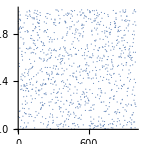
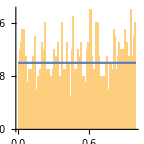
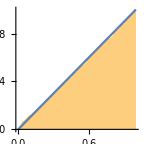
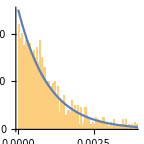
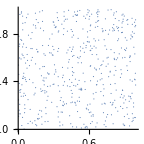
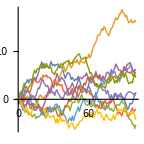
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.108634812347
Do not reject | 0.108855
Do not reject
AD | 0.07124554431
Do not reject | 0.097504
Do not reject
PC2 | 0.0900924084724
Do not reject | 0.1026332037
Do not reject |

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=RandomReal[1,1000,WorkingPrecision->16];
res=testRNG[xi]
Export["RNGtest-Mathematica.png",res,ImageResolution->600];
```

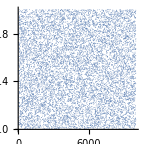
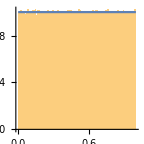
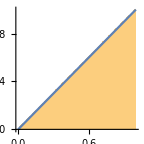
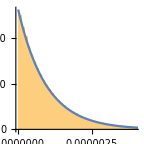
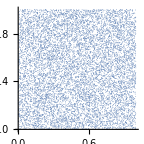
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.931192
Do not reject | 0.929628
Do not reject
AD | 0.868536
Do not reject | 0.
Reject
PC2 | 0.89082
Do not reject | 6.93596×10^-94
Reject |

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937.tst",Real];xi=xi[[1;;testSize]];
res=testRNG[xi]
Export["RNGtest-MT19937.png",res,ImageResolution->600];
```

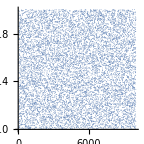
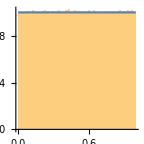
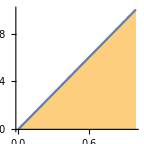
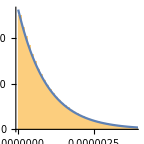
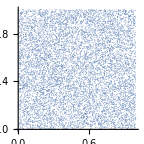
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.31867
Do not reject | 0.746598
Do not reject
AD | 0.240141
Do not reject | 0.680281
Do not reject
PC2 | 0.761035
Do not reject | 0.325944
Do not reject |

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937x64.tst",Real];xi=xi[[1;;testSize]];
res=testRNG[xi]
Export["RNGtest-MT19937x64.png",res,ImageResolution->600];
```

```mathematica
testRNG[xi]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.160241
Do not reject | 0.879698
Do not reject
AD | 0.225544
Do not reject | 0.849009
Do not reject
PC2 | 0.650031
Do not reject | 0.883012
Do not reject |

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms2203.tst",Real];xi=Partition[xi,1024];
walks=Table[Accumulate[2xi[[i]]-1],{i,1,6024}];
Manipulate[
ListLinePlot[walks[[a;;b,1;;n]],PlotRange->{All,{Min[walks[[a;;b,1;;n]]],Max[walks[[a;;b,1;;n]]]}},AspectRatio->1,PlotStyle->Thin,ImageSize->72*6],
{{a,1},1,6024,1},
{{b,5},1,6024,1},
{{n,1024},1,1024,1}]
```